```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA_CT",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs}];
```

## g-g- t- t (1-loop - self energy)

```mathematica
topsCT = CreateCTTopologies[1,2->2,ExcludeTopologies->{WFCorrectionCTs,TadpoleCTs,BoxCTs,TriangleCTs}];
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrections}];
processGGT =  { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[topsCT,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA_CT} initialized

in total: 59 Particles insertions

```mathematica
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->True,SMP->True,LorentzIndexNames-> {μ,ν},Contract->True,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings//.{GS->gs}),ChangeDimension->D]/.{GS->gs};
nonZero={};
(* Keep only the diagrams up to gs^2 and containing yDM *)
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	M=Normal[Series[M,{gs,0,2}]];
	M=Normal[Series[M,{yDM,0,2}]];
	M=DiracSimplify[M];
    If[!M==={0} && !FreeQ[M,yDM] ,AppendTo[nonZero,n]];
];
```

in total: 59 Particles amplitudes

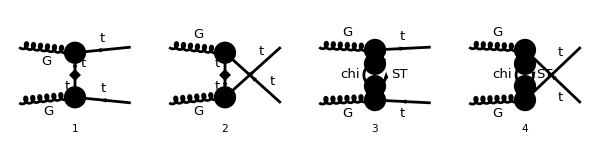

```mathematica
goodDiags=DiagramExtract[allDiags,nonZero];
(* goodDiags=DiagramExtract[goodDiags,{2,3,6,7,8,9}]; *)
(* goodDiags=DiagramExtract[goodDiags,{4,10,11}]; *)
goodDiags=DiagramExtract[goodDiags,{1,2,11,12}];
Paint[goodDiags,ColumnsXRows->{4,1},ImageSize->{ 600,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},LorentzIndexNames->{μ,ν},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
```

in total: 4 Particles amplitudes

```mathematica
(* Select only leading order *)
ampB=gs^2 yDM^2 FullSimplify[Coefficient[Coefficient[SUNSimplify[DiracSimplify[ampA]],yDM,2],gs,2]];
```

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]);
```

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

## On - Shell Case

since we are only interested in q q -> tt or gg -> tt, the t - t - g - g vertex only contributes when all external particles are on - shell, so we make use of this to simplify the final expressions

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MT,MT,0,0];
```

```mathematica
ampEsimp2=Simplify[DiracSimplify[ampEsimp]]/.{s+t+u-> 2 MT^2};
```

```mathematica
subs = {DiracGamma[Momentum[p2,D],D].DiracGamma[Momentum[k2,D],D]->-DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[p2,D],D]+2SPD[k2,p2],DiracGamma[Momentum[p1,D],D].DiracGamma[Momentum[k2,D],D]->-DiracGamma[Momentum[k2,D],D].DiracGamma[Momentum[p1,D],D]+2SPD[k2,p1]};
ampEsimp2=DiracSimplify[ampEsimp2/.subs];
```

## Check Divergences

```mathematica
allLoopInts = Cases2[ampEsimp2,{PaVe,A0,B0,C0,D0}];
```

```mathematica
Table[{allLoopInts[[i]],PaXEvaluateUV[allLoopInts[[i]],PaXImplicitPrefactor->1/(2 Pi)^(4)]},{i,1,Length[allLoopInts]}]
```

(A_0(mChi^2) | mChi^2/(16 π^4 ε_UV)
A_0(mST^2) | mST^2/(16 π^4 ε_UV)
B_0(t,mChi^2,mST^2) | 1/(16 π^4 ε_UV)
B_0(u,mChi^2,mST^2) | 1/(16 π^4 ε_UV))

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampEsimp2,PaXImplicitPrefactor->1/(2 Pi)^(4)]];
(* Divergences from counter-terms *)
ctUV=FullSimplify[SUNSimplify[Coefficient[ampEsimp2,deltaSp]] (-1/(32 Pi^4  EpsilonUV))];
FullSimplify[FeynAmpDenominatorExplicit[DiracSimplify[loopUV+ctUV,DiracSubstitute67->True]]]
```

0

## Coefficients for Loop Amplitude

```mathematica
subs2={B0[t,mChi^2,mST^2]->(ab[t]+(A0[mST^2]-A0[mChi^2]))/(mST^2-mChi^2-t),B0[u,mChi^2,mST^2]->(ab[u]+(A0[mST^2]-A0[mChi^2]))/(mST^2-mChi^2-u)};
```

```mathematica
ampEsimp3=FeynAmpDenominatorExplicit[DiracSimplify[ampEsimp2/.subs]]/.subs2;
```

```mathematica
spinorChains1=Tally[Cases[{ampEsimp3},DiracGamma[___],All]][[All,1]];
spinorChains2=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains3=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains4=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
allTerms=Sort[Join[spinorChains1,spinorChains2,spinorChains3,spinorChains4]]
su3prods=Join[Cases2[ampEsimp3,SUNTF],Cases2[ampEsimp3,SUNF]]
```

{(γ̄)^6,γ^μ,γ^ν,γ·k2,γ·p1,γ·p2,γ^μ.γ^ν,γ^ν.γ^μ,γ^μ.(γ·k2).γ^ν,γ^μ.(γ·p2).γ^ν,γ^ν.(γ·k2).γ^μ,γ^ν.(γ·p1).γ^μ,γ^μ.(γ·k2).γ^ν.(γ̄)^6,γ^μ.(γ·p2).γ^ν.(γ̄)^6,γ^ν.(γ·k2).γ^μ.(γ̄)^6,γ^ν.(γ·p1).γ^μ.(γ̄)^6}

{(T^Glu1 T^Glu2)_Col3Col4,(T^Glu2 T^Glu1)_Col3Col4}

### Coefficients for each term

Define shortnames for each coefficient

```mathematica
subs3={(-MT ab(t)+2 deltaS MT^2+4 deltaS t+2 deltaSp MT t)/(2 (MT^2-t)^2)-> ab1[s,t],(2 t (deltaS (2 MT^2+t)+deltaSp MT^3)-MT^3 ab(t))/(2 MT t (MT^2-t)^2)->ab2[s,t],(MT ab(t)+2 t (deltaS-deltaSp MT))/(2 MT t (MT^2-t))-> ab3[s,t],-(-MT ab(t)+2 deltaS MT^2+4 deltaS t+2 deltaSp MT t)/(2 (MT^2-t)^2)-> -ab1[s,t],-(2 t (deltaS (2 MT^2+t)+deltaSp MT^3)-MT^3 ab(t))/(2 MT t (MT^2-t)^2)->-ab2[s,t],-(MT ab(t)+2 t (deltaS-deltaSp MT))/(2 MT t (MT^2-t))-> -ab3[s,t]};
subs4={(-MT ab(u)+2 deltaS MT^2+4 deltaS u+2 deltaSp MT u)/(2 (MT^2-u)^2)-> ab1[s,u],(2 u (deltaS (2 MT^2+u)+deltaSp MT^3)-MT^3 ab(u))/(2 MT u (MT^2-u)^2)->ab2[s,u],(MT ab(u)+2 u (deltaS-deltaSp MT))/(2 MT u (MT^2-u))-> ab3[s,u],-(-MT ab(u)+2 deltaS MT^2+4 deltaS u+2 deltaSp MT u)/(2 (MT^2-u)^2)->- ab1[s,u],-(2 u (deltaS (2 MT^2+u)+deltaSp MT^3)-MT^3 ab(u))/(2 MT u (MT^2-u)^2)->-ab2[s,u],-(MT ab(u)+2 u (deltaS-deltaSp MT))/(2 MT u (MT^2-u))-> -ab3[s,u]};
```

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Coefficient[Expand[ampEsimp3],su3prods[[i]]],allTerms[[j]]]];
If[c==0,Continue[]];
c= Collect[c/(I Pi^2 gs^2 yDM^2),{MT,t,u},FullSimplify]/.Join[subs3,subs4];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]}];
```

#### Check that all terms have been correctly split

```mathematica
(* ampTot = I Pi^2 gs^2 yDM^2 Sum[su3Terms[[i,1]] su3Terms[[i,2]] su3Terms[[i,3]],{i,1,Length[su3Terms]}]; *)
(* Simplify[ampTot-ampEsimp3] *)
```

```mathematica
su3Terms
```

((T^Glu1 T^Glu2)_Col3Col4 | γ^μ.γ^ν | -ab1(s,t)
(T^Glu1 T^Glu2)_Col3Col4 | γ^μ.(γ·k2).γ^ν | -ab2(s,t)
(T^Glu1 T^Glu2)_Col3Col4 | γ^μ.(γ·p2).γ^ν | ab2(s,t)
(T^Glu1 T^Glu2)_Col3Col4 | γ^μ.(γ·k2).γ^ν.(γ̄)^6 | -ab3(s,t)
(T^Glu1 T^Glu2)_Col3Col4 | γ^μ.(γ·p2).γ^ν.(γ̄)^6 | ab3(s,t)
(T^Glu2 T^Glu1)_Col3Col4 | γ^ν.γ^μ | -ab1(s,u)
(T^Glu2 T^Glu1)_Col3Col4 | γ^ν.(γ·k2).γ^μ | ab2(s,u)
(T^Glu2 T^Glu1)_Col3Col4 | γ^ν.(γ·p1).γ^μ | -ab2(s,u)
(T^Glu2 T^Glu1)_Col3Col4 | γ^ν.(γ·k2).γ^μ.(γ̄)^6 | ab3(s,u)
(T^Glu2 T^Glu1)_Col3Col4 | γ^ν.(γ·p1).γ^μ.(γ̄)^6 | -ab3(s,u))

## Construct ALOHA terms

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g, P.g ] ] = [ -p2=P(*,1),  -p1=P(*,2),  k1(μ)=P(*,3),  k2(ν)=P(*,4) ] (all momenta are incoming)
Col3 = Top color = "2", Col4 = Anti-Top color = "1", Glu1->k1(mu) = "3", Glu2->k2(nu) = "4"
spins = [2, 2, 3, 3], 
structure = ' P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)')

t = (p1-k1)^2  = (k1-p1)^2 = P(-1,3)**2 + P(-1,2)**2 + 2*P(-1,3)*P(-1,2)
u = (p1-k2)^2  = (k2-p1)^2 = P(-1,4)**2 + P(-1,2)**2 + 2*P(-1,4)*P(-1,2)

```mathematica
su3Matrices=Tally[su3Terms[[All,1]]][[All,1]]
tensors=Tally[su3Terms[[All,2]]][[All,1]]
```

{(T^Glu1 T^Glu2)_Col3Col4,(T^Glu2 T^Glu1)_Col3Col4}

{γ^μ.γ^ν,γ^μ.(γ·k2).γ^ν,γ^μ.(γ·p2).γ^ν,γ^μ.(γ·k2).γ^ν.(γ̄)^6,γ^μ.(γ·p2).γ^ν.(γ̄)^6,γ^ν.γ^μ,γ^ν.(γ·k2).γ^μ,γ^ν.(γ·p1).γ^μ,γ^ν.(γ·k2).γ^μ.(γ̄)^6,γ^ν.(γ·p1).γ^μ.(γ̄)^6}

```mathematica
Table[{tensors[[i]],InputForm[tensors[[i]]]},{i,1,Length[tensors]}];
```

```mathematica
su3Replacements={SUNTF[{SUNIndex[Glu1],SUNIndex[Glu2]},SUNFIndex[Col3],SUNFIndex[Col4]]-> "T(3,2,-1)*T(4,-1,1)",
                                   SUNTF[{SUNIndex[Glu2],SUNIndex[Glu1]},SUNFIndex[Col3],SUNFIndex[Col4]]->  "T(4,2,-1)*T(3,-1,1)"};
```

```mathematica
tensorReplacements={DiracGamma[LorentzIndex[μ,D],D].DiracGamma[LorentzIndex[ν,D],D]-> "Gamma(3,2,-1)*Gamma(4,-1,1)",
				   DiracGamma[LorentzIndex[ν,D],D].DiracGamma[LorentzIndex[μ,D],D]-> "Gamma(4,2,-1)*Gamma(3,-1,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[k2, D], D] . DiracGamma[LorentzIndex[ν, D], D]->  "Gamma(3,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(4,-3,1)",
DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[k2, D], D] . DiracGamma[LorentzIndex[μ, D], D]->  "Gamma(4,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(3,-3,1)",DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p2, D], D] . DiracGamma[LorentzIndex[ν, D], D]->  "Gamma(3,2,-1)*(-P(-2,1))*Gamma(-2,-1,-3)*Gamma(4,-3,1)",DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p1, D], D] . DiracGamma[LorentzIndex[μ, D], D]->  "Gamma(4,2,-1)*(-P(-2,2))*Gamma(-2,-1,-3)*Gamma(3,-3,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[k2, D], D] . DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[6]-> "Gamma(3,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1)",
DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[k2, D], D] . DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[6]-> "Gamma(4,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1)",DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p2, D], D] . DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[6]-> "Gamma(3,2,-1)*(-P(-2,1))*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1)",DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p1, D], D] . DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[6]-> "Gamma(4,2,-1)*(-P(-2,2))*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1)"};
```

```mathematica
tensorReplacements = SortBy[tensorReplacements,-StringLength[ToString[#]]&]
```

{γ^μ.(γ·p2).γ^ν.(γ̄)^6→Gamma(3,2,-1)*(-P(-2,1))*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1),γ^ν.(γ·p1).γ^μ.(γ̄)^6→Gamma(4,2,-1)*(-P(-2,2))*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1),γ^μ.(γ·k2).γ^ν.(γ̄)^6→Gamma(3,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1),γ^ν.(γ·k2).γ^μ.(γ̄)^6→Gamma(4,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1),γ^μ.(γ·p2).γ^ν→Gamma(3,2,-1)*(-P(-2,1))*Gamma(-2,-1,-3)*Gamma(4,-3,1),γ^ν.(γ·p1).γ^μ→Gamma(4,2,-1)*(-P(-2,2))*Gamma(-2,-1,-3)*Gamma(3,-3,1),γ^μ.(γ·k2).γ^ν→Gamma(3,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(4,-3,1),γ^ν.(γ·k2).γ^μ→Gamma(4,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(3,-3,1),γ^μ.γ^ν→Gamma(3,2,-1)*Gamma(4,-1,1),γ^ν.γ^μ→Gamma(4,2,-1)*Gamma(3,-1,1)}

### Print each Lorentz structure as a distinct Lorentz vertex :

```mathematica
vertexCounter=20;
Do[
Print["------------------"];
Print[su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
If[Length[terms1]==0,Continue[]];
vertexCounter += 1;
Print[StringJoin["FFVVNP",ToString[vertexCounter]]];
(* Print[tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=StringJoin["(",ToString[FortranForm[terms1[[1,3]]]],")"];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*(",fullStr,")"];
 Print[fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
```

------------------

T(3,2,-1)*T(4,-1,1)

FFVVNP21

( Gamma(3,2,-1)*Gamma(4,-1,1) )*((-ab1(s,t)))

FFVVNP22

( Gamma(3,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(4,-3,1) )*((-ab2(s,t)))

FFVVNP23

( Gamma(3,2,-1)*(-P(-2,1))*Gamma(-2,-1,-3)*Gamma(4,-3,1) )*((ab2(s,t)))

FFVVNP24

( Gamma(3,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1) )*((-ab3(s,t)))

FFVVNP25

( Gamma(3,2,-1)*(-P(-2,1))*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1) )*((ab3(s,t)))

------------------

T(4,2,-1)*T(3,-1,1)

FFVVNP26

( Gamma(4,2,-1)*Gamma(3,-1,1) )*((-ab1(s,u)))

FFVVNP27

( Gamma(4,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(3,-3,1) )*((ab2(s,u)))

FFVVNP28

( Gamma(4,2,-1)*(-P(-2,2))*Gamma(-2,-1,-3)*Gamma(3,-3,1) )*((-ab2(s,u)))

FFVVNP29

( Gamma(4,2,-1)*P(-2,4)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1) )*((ab3(s,u)))

FFVVNP30

( Gamma(4,2,-1)*(-P(-2,2))*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1) )*((-ab3(s,u)))

#### Write to File

```mathematica
fileName="../../Models/Top-FormFactorsOneLoop-UFO/lffvvnpSelf.txt";
outF = OpenWrite[fileName,PageWidth->Infinity];
vertexCounter=20;
Do[
Write[outF,"------------------"];
Write[outF,su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
If[Length[terms1]==0,Continue[]];
vertexCounter += 1;
Write[outF,StringJoin["FFVVNP",ToString[vertexCounter]]];
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=StringJoin["(",ToString[FortranForm[terms1[[1,3]]]],")"];
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*( ",fullStr,")"];
 Write[outF,fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
Close[outF]
```

../../Models/Top-FormFactorsOneLoop-UFO/lffvvnpSelf.txt